# Pursuit Problems

## Extra

```mathematica
Duck=Image[ImageTrim[Import["http://i.imgur.com/M8OcQEL.png"],{{0,0},{300,300}}],ImageSize->40];
Dog=Image[Import["http://img2.wikia.nocookie.net/__cb20140518092211/mugen/images/0/00/Doge-head.png"],ImageSize-> 25];
Clops=Image[Import["/Users/Miguel/Desktop/Physics 411 (Non-linear Dynamics and Chaos)/Clops.png"],ImageSize-> 30];
```

```mathematica
red=ColorData["DarkRainbow",0.9];
orange=Orange;
yellow=ColorData["DarkRainbow",0.65];
green=ColorData["DarkRainbow",0.45];
purple=ColorData["Rainbow",0.01];
```

## Hathaway’s Pursuit Problem

A dog at the center of a circular pond makes straight for a duck which is swimming [counterclockwise] along the edge of the circular pond of unit radius. If the rate of swimming of the dog is to the rate of swimming of the duck as k:1, determine the equation of the curce of pursuit and the distance the dog swims to catch the duck.

Since we have already found the analytical solution (or at least come as close as possible), we will now attack this problem from a standpoint.

From Nahin, we know that we can represent the velocity of the dog in the x and y directions as:

```mathematica
vx[x_,y_,t_]:= (k (Cos[t]-x))/(√((Cos[t]-x)^2+(Sin[t]-y)^2));
vy[x_,y_,t_]:= (k (Sin[t]-y))/(√((Cos[t]-x)^2+(Sin[t]-y)^2));
```

### k = 0.95

We’ll start with k = 0.95, and we’ll solve the above two equations with NDSolve. Let’s begin by assuming that the dog starts at the center of the pond (x_0 = y_0 = 0). Then define

```mathematica
dogpath[k_,x0_,y0_]:=NDSolve[{x'[t]== (k (Cos[t]-x[t]))/(√((Cos[t]-x[t])^2+(Sin[t]-y[t])^2)),y'[t]==(k (Sin[t]-y[t]))/(√((Cos[t]-x[t])^2+(Sin[t]-y[t])^2)),x[0]==x0,y[0]==y0},{x,y},{t,0,30}];
```

```mathematica
path=dogpath[0.95,0,0];
```

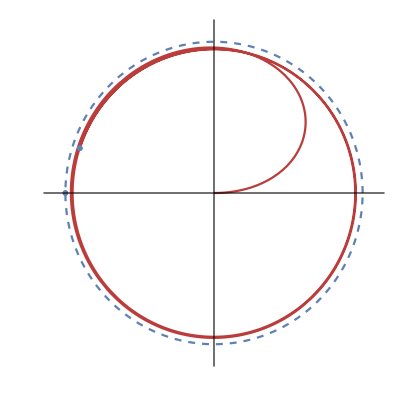

```mathematica
Show[ParametricPlot[{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},Ticks-> {None}, PlotStyle->Dashed,PlotRange->{{-1.1,1.1},{-1.1,1.1}}],ParametricPlot[Evaluate[{x[t],y[t]}/.path],{t,0,5π}, PlotStyle-> {red}],
ListPlot[Evaluate[{x[5π],y[5π]}/.path], PlotMarkers-> Dog],ListPlot[{{Cos[5π],Sin[5π]}},AspectRatio->Automatic,PlotMarkers->Duck ]]
```

### Limit Cycles

So it appears that we get doge following a constant ciruclar path. Does this circle depend on his velocity? Let’s look back and compare the different values of k, and look from times t = 6π to t = 8π, and  we get

```mathematica
path75=dogpath[0.75,0,0];
path5=dogpath[0.5,0,0];path3=dogpath[0.3,0,0];
```

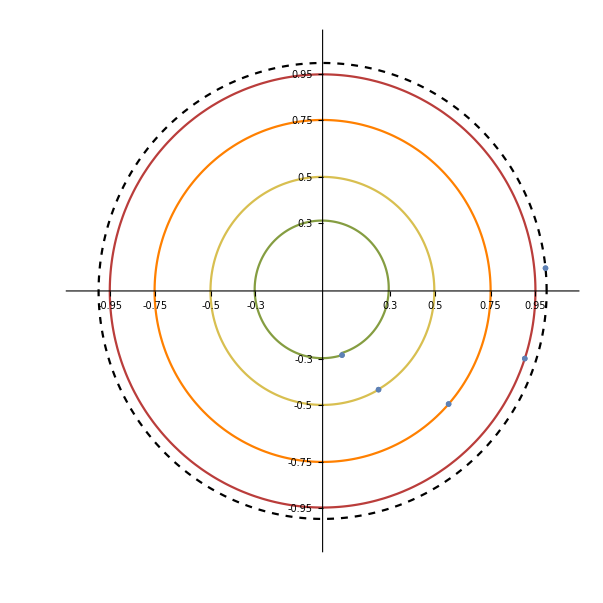

```mathematica
limitc=Show[ParametricPlot[{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},Ticks-> {{0.3,0.5,0.75,0.95,-0.3,-0.5,-0.75,-0.95}}, PlotStyle->{Dashed,Black},AxesStyle-> Large,PlotRange->{{-1.1,1.1},{-1.1,1.1}}],ListPlot[{{Cos[8π+.1],Sin[8π+.1]}},AspectRatio->Automatic, PlotMarkers-> Duck ],ParametricPlot[Evaluate[{x[t],y[t]}/.path],{t,6π,8π}, PlotStyle-> {red}],
ListPlot[Evaluate[{x[8π],y[8π]}/.path], PlotMarkers-> Dog],
ParametricPlot[Evaluate[{x[t],y[t]}/.path75],{t,6π,8π}, PlotStyle-> {orange}],
ListPlot[Evaluate[{x[8π],y[8π]}/.path75], PlotMarkers-> Dog],ParametricPlot[Evaluate[{x[t],y[t]}/.path5],{t,6π,8π}, PlotStyle-> {yellow}],
ListPlot[Evaluate[{x[8π],y[8π]}/.path5], PlotMarkers-> Dog],
ParametricPlot[Evaluate[{x[t],y[t]}/.path3],{t,6π,8π}, PlotStyle-> {green}],
ListPlot[Evaluate[{x[8π],y[8π]}/.path3], PlotMarkers-> Dog]]
```

Looks like doge gets stuck in a limit cycle! And here we can see that the radius of their limit cycle is exactly their value of k. This happens because the pond has unit radius.

### Non-Zero Initial Conditions

Let’s start doge way out there, and see what happens. We’re keeping k constant at k = 0.3.

```mathematica
nzpath75={dogpath[0.3,0.5,-0.5],dogpath[0.3,1,1], dogpath[0.3,1.5,-1.5]};
```

```mathematica
Animate[Show[ParametricPlot[{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},Ticks-> {None}, PlotStyle->Dashed,PlotRange->{{-1.5,1.5},{-1.5,1.5}}],
ParametricPlot[Evaluate[{x[t],y[t]}/.nzpath75],{t,0,T}],ListPlot[Evaluate[{x[T],y[T]}/.nzpath75], PlotMarkers-> Dog],ListPlot[{{Cos[T],Sin[T]}},AspectRatio->Automatic,PlotMarkers->Duck ]],{T,0,9π}, AnimationRate->0.045]
```

## Other Analysis

The differential equations are:

dR/dθ = sinϕ - k
dϕ/dθ = cosϕ/R-1

```mathematica
Manipulate[Show[StreamPlot[{(Cos[ϕ]/R-1),(Sin[ϕ]-k)},{ϕ,-3.14,3.14},{R,-1,1.5},FrameTicks->{{-π/2,π/2,π,-π,0},{1,1.5,0.5,{Abs[√(1-k^2)],"√(1 - SuperscriptBox[k, 2])"},0}},StreamScale-> Large, FrameLabel-> {"ϕ","R"}],Plot[√(1-k^2),{ϕ,-π,π}],
Plot[Cos[ϕ],{ϕ,0,π}]
],{{k,0.5},0,1}]
```

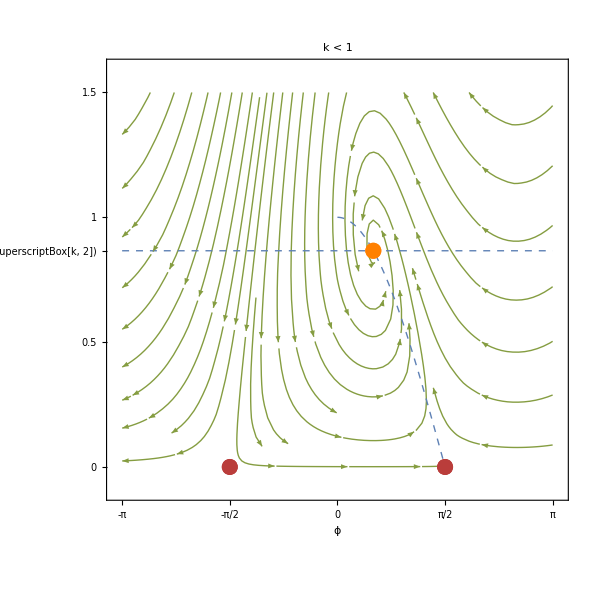

```mathematica
k=0.5;
streamplot=Show[StreamPlot[{(Cos[ϕ]/R-1),(Sin[ϕ]-k)},{ϕ,-3.14,3.14},{R,0,1.5},StreamStyle->{green,Thick},PlotLabel-> Style["k < 1",Large],FrameTicks->{{-π/2,π/2,π,-π,0},{1,1.5,0.5,{√(1-k^2),"√(1 - SuperscriptBox[k, 2])"},0}},FrameStyle-> Large, FrameLabel-> {"ϕ","R"},StreamScale-> Large],Plot[√(1-k^2),{ϕ,-π,π},PlotStyle->{Thick,Dashed}],
Plot[Cos[ϕ],{ϕ,0.0,π/2},PlotStyle->{Thick,Dashed}],ListPlot[{{ArcCos[√(1-k^2)],√(1-k^2)}},PlotStyle->{orange}],ListPlot[{{-π/2,0}},PlotStyle->{red}],
ListPlot[{{π/2,0}},PlotStyle->{red}]
]
```

Stable fixed point is the limit cylce.

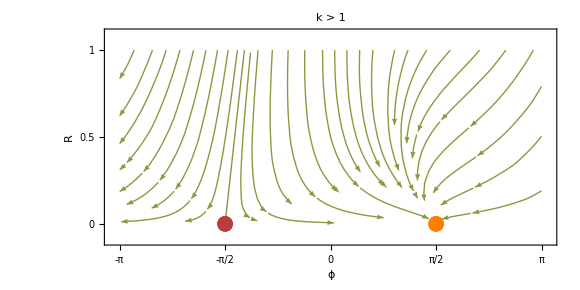

```mathematica
k=1.5;
streamplotgreater=Show[StreamPlot[{(Cos[ϕ]/R-1),(Sin[ϕ]-k)},{ϕ,-3.14,3.14},{R,0,1},AspectRatio-> 0.5,StreamStyle->{green,Thick},FrameTicks->{{-π/2,π/2,π,-π,0},{1,1.5,0.5,0}},FrameStyle-> Large, FrameLabel-> {"ϕ","R"},StreamScale-> Large,PlotLabel-> Style["k > 1",Large]],
ListPlot[{{-π/2,0}},PlotStyle->{red}],
ListPlot[{{π/2,0}},PlotStyle->{orange}]
]
```

Stable fixed point is caputre from behind. Frontal capture is saddle point.